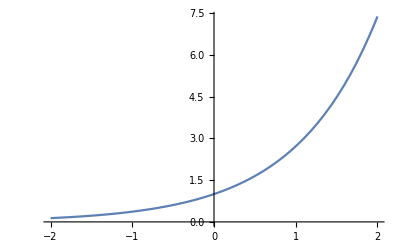

```mathematica
p1 = Plot[E^x,{x,-2,2}, PlotStyle-> "ThickLines", Ticks -> None]
```

```mathematica
peeters`exportForLatex[ "l8exponentialFig1", p1]
```

{l8exponentialFig1.eps,l8exponentialFig1pn.png}

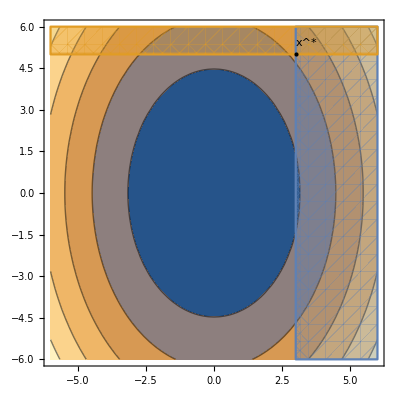

```mathematica
p2 = Show[{ContourPlot[ 2 x^2 + y^2, {x,-6,6}, {y, -6,6}],
RegionPlot[ {x ≥ 3, y ≥ 5},{x,-6,6}, {y, -6,6}],
Graphics[{
PointSize[Large],
Point[{3,5}],
Text[SuperStar[Style["x", Bold]],{3.4,5.4}]
}
]
}]
```

```mathematica
peeters`exportForLatex[ "l8constrainedMinFig2", p2]
```

{l8constrainedMinFig2.eps,l8constrainedMinFig2pn.png}

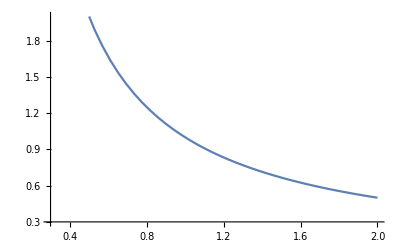

```mathematica
p6 = Plot[1/x,{x,0,2}, PlotStyle-> "ThickLines", Ticks -> None, PlotRange -> {{0.3,2},{0.3,2}}]
```

```mathematica
peeters`exportForLatex[ "l8oneOverXFig6", p6]
```

{l8oneOverXFig6.eps,l8oneOverXFig6pn.png}

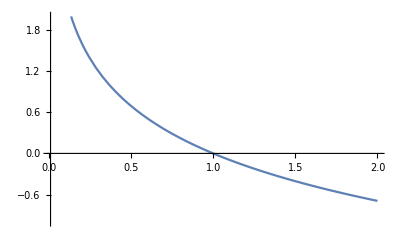

```mathematica
p7 = Plot[-Log[x],{x,0,2}, PlotStyle-> "ThickLines", Ticks -> None, PlotRange -> {{0.01,2},{-1,2}}]
```

```mathematica
peeters`exportForLatex[ "l8MinusLogXFig7", p7]
```

{l8MinusLogXFig7.eps,l8MinusLogXFig7pn.png}